```mathematica
Style["5. Design example",Bold]
Vi1=12;
Vi2=24;
D1=0.2;
D2=0.8;

Style["5.1 Região Buck",Bold]
VominBuck=D1*Vi2;
"VominBuck = "<>ToString[VominBuck]
VomaxBuck=D2*Vi2;
"VomaxBuck = "<>ToString[VomaxBuck]
Vi2/VomaxBuck<VVbuck<Vi2/VominBuck
Vobuck1=Vi1/(Vi2/VomaxBuck);
"Vobuck1 = "<>ToString[Vobuck1]
Vobuck2=Vi2/(Vi2/VomaxBuck);
"Vobuck2 = "<>ToString[Vobuck2]

Style["5.2 Região Boost",Bold]
VominBoost=Vi1/(1-D1);
"VominBoost = "<>ToString[VominBoost]
VomaxBoost=Vi2/(1-D2);
"VomaxBoost = "<>ToString[VomaxBoost]
Vi2/VomaxBoost<VVboost<Vi1/VominBoost
Voboost1=Vi1/(Vi1/VominBoost);
"Voboost1 = "<>ToString[Voboost1]
Voboost2=Vi2/(Vi1/VominBoost);
"Voboost2 = "<>ToString[Voboost2]
```

5. Design example

5.1 Região Buck

VominBuck = 4.8

VomaxBuck = 19.2

1.25<VVbuck<5.

Vobuck1 = 9.6

Vobuck2 = 19.2

5.2 Região Boost

VominBoost = 15.

VomaxBoost = 120.

0.2<VVboost<0.8

Voboost1 = 15.

Voboost2 = 30.

5.3 Regiões de operação

Região Buck > 1.25

Vi = [12,24]

Vo = [12,19.2]

0.8 <= Região Buck-Boost <= 1.25

Vi = [12,24]

Vo = [9.6,30.]

Região Boost < 0.8

Vi = [12,24]

Vo = [15.,24]

5.3.1 Regiões de operação

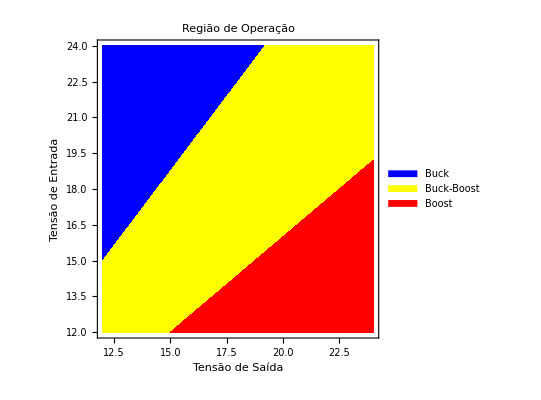

0.2 <= Vi/Vo <= 5.

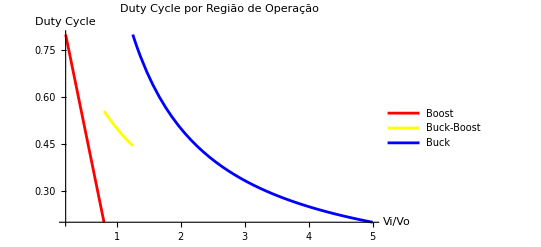

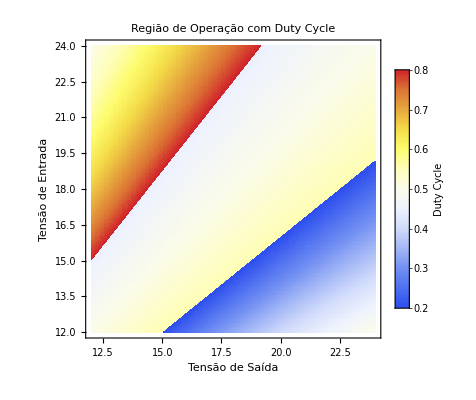

```mathematica
Style["5.3 Regiões de operação",Bold]
Vomin=12;
Vomax=24;
"Região Buck > "<>ToString[Vi2/VomaxBuck]
"Vi = ["<>ToString[Vi1]<>","<>ToString[Vi2]<>"]"
"Vo = ["<>ToString[Vomin]<>","<>ToString[VomaxBuck]<>"]"
ToString[Vi1/VominBoost]<>" <= Região Buck-Boost <= "<>ToString[Vi2/VomaxBuck]
"Vi = ["<>ToString[Vi1]<>","<>ToString[Vi2]<>"]"
"Vo = ["<>ToString[Vobuck1]<>","<>ToString[Voboost2]<>"]"
"Região Boost < "<>ToString[Vi1/VominBoost]
"Vi = ["<>ToString[Vi1]<>","<>ToString[Vi2]<>"]"
"Vo = ["<>ToString[VominBoost]<>","<>ToString[Vomax]<>"]"

Style["5.3.1 Regiões de operação",Bold]
RegionPlot[
{y/x>Vi2/VomaxBuck,Vi1/VominBoost<=y/x<=Vi2/VomaxBuck,y/x<Vi1/VominBoost},
{x,Vomin,Vomax},
{y,Vi1,Vi2},
PlotStyle->{Blue,Yellow,Red},
BoundaryStyle->None,
FrameLabel->{"Tensão de Saída","Tensão de Entrada"},
PlotLabel->"Região de Operação",
PlotLegends->{"Buck","Buck-Boost","Boost"}]

ToString[Vi2/VomaxBoost]<>" <= Vi/Vo <= "<>ToString[Vi2/VominBuck]

Plot[
{Piecewise[{{1-x,x<Vi1/VominBoost},{Indeterminate,True}}],
Piecewise[{{1/(1+x),Vi1/VominBoost<=x<=Vi2/VomaxBuck},{Indeterminate,True}}],
Piecewise[{{1/x,x>Vi2/VomaxBuck},{Indeterminate,True}}]},
{x,Vi2/VomaxBoost,Vi2/VominBuck},
PlotStyle->{Red,Yellow,Blue},
AxesLabel->{"Vi/Vo","Duty Cycle"},
PlotLabel->"Duty Cycle por Região de Operação",
PlotLegends->{"Boost","Buck-Boost","Buck"}]

DensityPlot[
Piecewise[{
{x/y,y/x>Vi2/VomaxBuck},
{x/(x+y),Vi1/VominBoost<=y/x<=Vi2/VomaxBuck},
{(x-y)/x,y/x<Vi1/VominBoost}}],
{x,Vomin,Vomax},
{y,Vi1,Vi2},
ColorFunction->"TemperatureMap",
PlotLegends->BarLegend[{"TemperatureMap",{D1,D2}},
LegendLabel->"Duty Cycle",Ticks->Range[0,1,0.1]],
FrameLabel->{"Tensão de Saída","Tensão de Entrada"},
PlotLabel->"Região de Operação com Duty Cycle",
RegionFunction->Function[{x,y},Vomin<=x<=Vomax&&Vi1<=y<=Vi2],PlotPoints->64]
```

```mathematica
Style["5.4 Cálculo dos componentes",Bold]
Io=2;
f=500;
Lr=0.6;
Vr=1;

Style["5.4.1 Buck",Bold]
Lmax[Vi_,Vo_]:=1/(f*Lr)(Vo-Vo^2/Vi);
Lbuckmax=NMaximize[{Lmax[Vi,Vo],Vi1<=Vi<=Vi2,Vomin<=Vo<=VomaxBuck},{Vi,Vo}];
"Lmax = "<>ToString[EngineeringForm[Lbuckmax]]
Cbuck=Lr/(8*f*Vr);
"C = "<>ToString[EngineeringForm[Cbuck]]

Style["5.4.2 Buck-Boost",Bold]
Lbbmax=1/(f*Lr)*Voboost2/(1+(Voboost2/Vi2));
"Lmax = "<>ToString[EngineeringForm[Lbbmax]]
Cbb=Io/(f*Vr)*Voboost2/(Voboost2+Vi1);
"C = "<>ToString[EngineeringForm[Cbb]]

Style["5.4.3 Buck-Boost",Bold]
Lmax[Vi_,Vo_]:=1/(f*Lr)*(Vi-Vi^2/Vo);
Lboostmax=NMaximize[{Lmax[Vi,Vo],Vi1<=Vi<=Vi2,VominBoost<=Vo<=Vomax},{Vi,Vo}];
"Lmax = "<>ToString[EngineeringForm[Lboostmax]]
Cboost=Io/(f*Vr)*(Vomax-Vi1)/Vomax;
"C = "<>ToString[EngineeringForm[Cboost]]

Lmaxmax=Max[Lbuckmax,Lbbmax,Lboostmax];
"Lmaxmax = "<>ToString[EngineeringForm[Lmaxmax]]
Cmaxmax=Max[Cbuck,Cbb,Cboost];
"Cmaxmax = "<>ToString[EngineeringForm[Cmaxmax]]
```

5.4 Cálculo dos componentes

5.4.1 Buck

Lmax =          -3
{20. × 10  , {Vi -> 24., Vo -> 12.0037}}

C =          -6
150. × 10

5.4.2 Buck-Boost

Lmax =             -3
44.4444 × 10

C =             -3
2.85714 × 10

5.4.3 Buck-Boost

Lmax =          -3
{20. × 10  , {Vi -> 12.0052, Vo -> 24.}}

C =  1
---
500

Lmaxmax =                 -3
Max[44.4444 × 10  , Vi -> 12.0052, Vi -> 24., Vo -> 12.0037, Vo -> 24.]

Cmaxmax =             -3
2.85714 × 10

```mathematica
Style["5.4 Verification",Bold]
Style["5.4.1 Buck",Bold]
Solve[Lmaxmax[[1]]==1/(f*Lr1)*((Vo/.Lbuckmax[[2]])-(Vo/.Lbuckmax[[2]])^2/Vi2),Lr1]
Solve[Cmaxmax==(Lr1/.%[[1]])/(8*f*Vr1),Vr1]

Style["5.4.1 Buck-Boost",Bold]
Solve[Lmaxmax[[1]]==1/(f*Lr2)*Voboost2/(1+(Voboost2/Vi2)),Lr2]
Solve[Cmaxmax==Io/(f*Vr2)*(Voboost2/(Voboost2+Vi1)),Vr2]

Style["5.4.1 Boost",Bold]
Solve[Lmaxmax[[1]]==1/(f*Lr3)*((Vi/.Lboostmax[[2]])-(Vi/.Lboostmax[[2]])^2/Vomax),Lr3]
Solve[Cmaxmax==Io/(f*Vr3)*(Vomax-Vi1)/Vomax,Vr3]
```

5.4 Verification

5.4.1 Buck

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Lr1→0.27}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Vr1→0.024975}}

5.4.1 Buck-Boost

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Lr2→0.6}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Vr2→1.}}

5.4.1 Boost

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Lr3→0.495}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Vr3→0.995636}}